```mathematica
trikotnik={{0,0},{5,1},{7,4}}
```

{{0,0},{5,1},{7,4}}

```mathematica
stranice[{AA_,BB_,CC_}]:={{BB,CC},{BB,AA},{AA,CC}} 
stranice[trikotnik]
```

{{{5,1},{7,4}},{{5,1},{0,0}},{{0,0},{7,4}}}

```mathematica
koti[{AA_,BB_,CC_}]:= {{AA,BB,CC},{BB,AA,CC},{AA,CC,BB}}
```

```mathematica
SlikaOglisc[trikotnik_]:=Map[Point,trikotnik] ;
SlikaStranice[trikotnik_]:= Map[Line,stranice[trikotnik]];
NarisiTrikotnik[trikotnik_]:=Graphics[{PointSize[Large],SlikaOglisc[trikotnik],{Blue,SlikaStranice[trikotnik]}}, AspectRatio->Automatic]
```

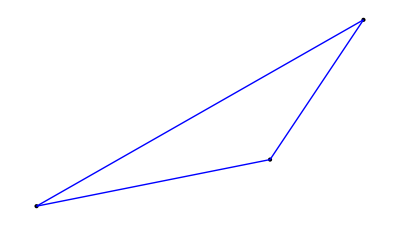

```mathematica
NarisiTrikotnik[trikotnik]
```

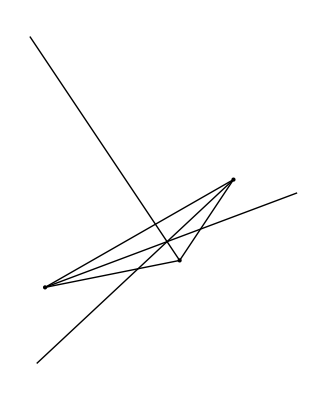

```mathematica
VektorSimetraleKota[{x_,y_,z_}]:=Normalize[Normalize[x-y]+Normalize[z-y]]
SimetralaKota[{x_,y_,z_},dol_:10]:={y,y+VektorSimetraleKota[{x,y,z}]*dol}
SlikaSimetraleKotov[trikotnik_]:=Map[Line,Map[SimetralaKota,koti[trikotnik]]];
ClearAll[NarisiTrikotnik]
NarisiTrikotnik[trikotnik_,OptionsPattern[Simetrale->False]]:= Module[{slike},
slike={PointSize[Large],SlikaOglisc[trikotnik],SlikaStranice[trikotnik]};
If [OptionValue[Simetrale] == True, AppendTo[slike,SlikaSimetraleKotov[trikotnik]]];
Graphics[slike,AspectRatio->Automatic]]
NarisiTrikotnik[trikotnik,Simetrale->True]
```

4.Naloga

```mathematica
e1={AA,BB}
e2={AA,CC}
PresecisceSimetral[{AA_,BB_,CC_}]:=Module[{}
```